## Input

## Refine bounding box

Bounding box is a list of pairs. Every pair consists of limits {min, max} for every parameter

```mathematica
FindInnerBox[bbox_,samples_,mask_]:=
MapThread[
{Max[#1⟦1⟧,#2⟦1⟧],Min[#1⟦2⟧,#2⟦2⟧]}&,
{
bbox,
{Min[#],Max[#]}&/@Transpose@Pick[samples,mask]
}];
```

```mathematica
MaxFromList[list_,default_]:=If[Length[list]==0,default,Max[list]]
MinFromList[list_,default_]:=If[Length[list]==0,default,Min[list]]
```

```mathematica
FindOuterBox[bbox_,samples_,mask_]:=
If[
And@@mask,
bbox,
MapThread[
Function[
{
paramSamples,
inLimits,
outLimits
},
{
MaxFromList[Select[paramSamples,#<inLimits⟦1⟧&],outLimits⟦1⟧],
MinFromList[Select[paramSamples,#>inLimits⟦2⟧&],outLimits⟦2⟧]
}],
{
Transpose@Pick[samples,mask,False],
FindInnerBox[bbox,samples,mask],
bbox
}
]
]
```

## Metric

Check that a sample in a box

```mathematica
InClosedBoxQ[sample_,bbox_]:=And@@MapThread[(#2⟦1⟧≤#1)&&(#1≤#2⟦2⟧)&,{sample,bbox}]
InOpenBoxQ[sample_,bbox_]:=And@@MapThread[(#2⟦1⟧<#1)&&(#1<#2⟦2⟧)&,{sample,bbox}]
```

Find ration of correct/total in bounding box

```mathematica
FindRecall[bbox_,samples_,mask_]:=
Module[
{
inBoxMask=Map[InOpenBoxQ[#,bbox]&,samples]
},
N@Count[MapThread[And,{inBoxMask,mask}],True]/Count[inBoxMask,True]
]
```

## Splitting

```mathematica
ClearAll[FindSplittingThreshold,SplitBBox]
```

```mathematica
FindSplittingThreshold[{bbox_,samples_,mask_},idx_]:=
Module[
{
inBoxMask=Map[InOpenBoxQ[#,bbox]&,samples],
values
},
values=Map[#⟦idx⟧&,Pick[samples,inBoxMask]];
FindThreshold[Pick[values,Pick[mask,inBoxMask]]]
]
```

```mathematica
SplitBBox[bbox_,threshold_,idx_]:=
{
ReplacePart[bbox,idx->{bbox⟦idx,1⟧,threshold}],
ReplacePart[bbox,idx->{threshold,bbox⟦idx,2⟧}]
}
```

## Refine State

```mathematica
ClearAll[NarrowState,RefineState]

NarrowState=Function[{bbox,samples,mask},
{bbox,Pick[samples,#],Pick[mask,#]}&[Map[InOpenBoxQ[#,bbox]&,samples]]
];
RefineState=Function[{bbox,samples,mask},
NarrowState[FindOuterBox[bbox,samples,mask],samples,mask]
];
```

```mathematica
SplitState=
Function[{state,splitIndex},
Module[
{
splitThreshold,
splitBoxes
},
If[
And@@state⟦3⟧,
{state},
splitThreshold=FindSplittingThreshold[state,splitIndex];
splitBoxes=SplitBBox[state⟦1⟧,splitThreshold,splitIndex];
{
RefineState@@NarrowState[splitBoxes⟦1⟧,state⟦2⟧,state⟦3⟧],
RefineState@@NarrowState[splitBoxes⟦2⟧,state⟦2⟧,state⟦3⟧]
}
]
]
];
```

## Picture

```mathematica
colors=ColorData[94,"ColorList"];
```

```mathematica
PlotState[bbox_,samples_,mask_]:=
Module[
{
inBox=FindInnerBox[bbox,samples,mask],
outBox=FindOuterBox[bbox,samples,mask]
},
Graphics[
{
{FaceForm[Directive[colors⟦1⟧,Opacity[0.25]]],EdgeForm[None],Rectangle@@Transpose[outBox]},
{Orange,PointSize-> Medium,Point[Pick[samples,mask]]},
{Blue,PointSize-> Medium,Point[Pick[samples,mask,False]]},
{FaceForm[None],EdgeForm[colors⟦1⟧],Rectangle@@Transpose[bbox]}
}
]
]
```

```mathematica
PlotStates[states_,samples_,mask_]:=
Graphics[
Join[
Table[
{FaceForm[Directive[colors⟦1⟧,Opacity[0.25]]],EdgeForm[colors⟦1⟧],Rectangle@@Transpose[s⟦1⟧]},
{s,states}],
{
{Orange,PointSize-> Medium,Point[Pick[samples,mask]]},
{Blue,PointSize-> Medium,Point[Pick[samples,mask,False]]}
}
]
]
```

## Output

## Demo bounding box refinement

### Data

Objective function

```mathematica
f[x_,y_]:=4(x^2+y^2)(1-(x^2+y^2));
```

```mathematica
GetSamples[n_]:=Sqrt[#1]{Cos[2π #2],Sin[2π #2]}&@@@RandomReal[{0,1},{n,2}]
samples=GetSamples[288];
weights=f@@@samples;
mask=Thread[weights≥0.8];
```

### Bounding boxes

```mathematica
states={{{{-1,1},{-1,1}},samples,mask}};
```

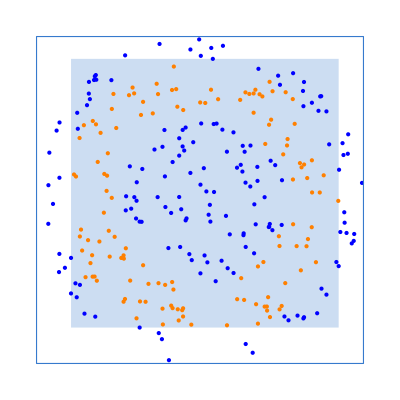

```mathematica
Show[PlotState@@@states]
```

```mathematica
states=RefineState@@@states;
```

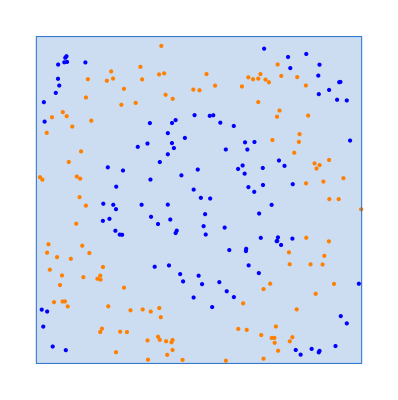

```mathematica
Show[PlotState@@@states]
```

```mathematica
FindRecall@@@states
```

{0.516129}

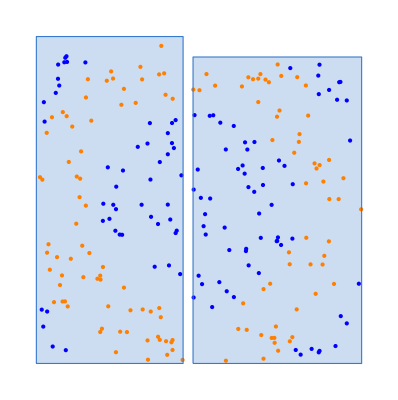

{0.588235,0.467742}

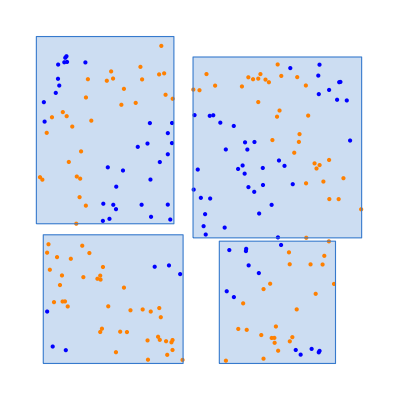

{0.869565,0.483871,0.648649,0.459459}

```mathematica
states=Join@@(SplitState[#,1]&/@states);
Show[PlotState@@@states]
FindRecall@@@states

states=Join@@(SplitState[#,2]&/@states);
Show[PlotState@@@states]
FindRecall@@@states
```

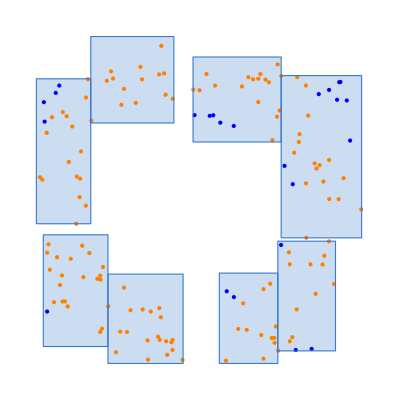

{0.952381,1.,0.8,1.,0.857143,0.8,0.761905,0.666667}

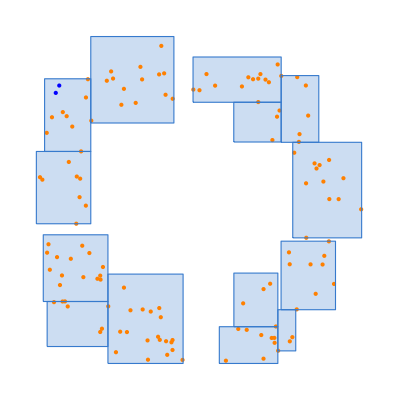

{1.,1.,1.,1.,0.8,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
states=Join@@(SplitState[#,1]&/@states);
Show[PlotState@@@states]
FindRecall@@@states

states=Join@@(SplitState[#,2]&/@states);
Show[PlotState@@@states]
FindRecall@@@states
```

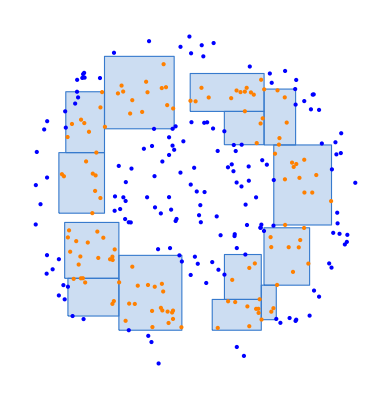

```mathematica
PlotStates[states,samples,mask]
```